# Using Timing function Homework 3 James Meeks and Valerie Richmond 12:40 and 8am CPS/Math 371

## 1.

i.

```mathematica
(*This Module is given three positive integers. It returns a list containing information (the x, y, x+y, and x*y) about every number x for which x+y=Reverse(x*y) between low and high, inclusive. This involves calling a function (checkInput) to check the x+y=Reverse(x*y) property for all x and y values in the appropriate range, and adding the information to the list for all values that have the property.*)

uPlusRevTimesOneX[x_, low_, high_] := Module[{xVal=x, end= high, resList={}, count=1, start=low, infoList={}},
 
 For[count=1, start≤high, start++, 
If[ checkInput[xVal, start], 
AppendTo[infoList, xVal];
AppendTo[infoList, start];
AppendTo[infoList, xVal+start];
AppendTo[infoList, start*xVal]; 
AppendTo[resList, infoList]];
infoList={}]; 
Return[resList]]
```

```mathematica
checkInput[xValue_, yValue_]:=Module[{x=xValue, y=yValue, reverse},
reverse=Reverse[IntegerDigits[x*y]];
reverse=FromDigits[reverse];
If[x+y==reverse, 
Return[True], 
Return[False]]
]
```

```mathematica
uPlusRevTimesOneX[2,1,100000]
```

{{2,2,4,4},{2,47,49,94},{2,497,499,994},{2,4997,4999,9994},{2,49997,49999,99994}}

```mathematica
uPlusRevTimesOneX[5,100,10000]
```

{{5,386,391,1930},{5,3986,3991,19930}}

ii.

```mathematica
(*This Module is given two positive integers and returns a list with information about all pairs with the property x+y=Reverse(x*y) between the low and high bounds given. It repeatedly calls the function for one pair created in part(i).*)

uPlusReverseTimes[low_, high_] :=Module[{start=low, resList={}, list={}, count, elem, finalList={}},
 For[start, start≤ high, start++, 
list=uPlusRevTimesOneX[start, start, high]; 
If[!Length[list]==0,
AppendTo[resList,  list] ]];
For[count=1, count≤Length[resList], count++ , 
If[Depth[resList[[count]]]>1, 
For[elem=1,elem≤Length[resList[[count]]], elem++, 
AppendTo[finalList, resList[[count, elem]]]
], 
AppendTo[finalList, resList[[count]] ] 
]
 ]; 
Return[finalList]
]
```

```mathematica
uPlusReverseTimes[1, 10000]
```

{{2,2,4,4},{2,47,49,94},{2,497,499,994},{2,4997,4999,9994},{3,24,27,72},{5,26,31,130},{5,386,391,1930},{5,3986,3991,19930},{8,455,463,3640},{9,9,18,81},{11,110,121,1210},{15,228,243,3420},{15,624,639,9360},{15,2568,2583,38520},{21,600,621,12600},{23,170,193,3910},{35,212,247,7420},{44,2255,2299,99220},{51,300,351,15300},{60,9615,9675,576900},{75,2616,2691,196200},{86,800,886,68800},{99,990,1089,98010},{150,4296,4446,644400},{180,2835,3015,510300},{225,4104,4329,923400},{528,1650,2178,871200},{1320,4125,5445,5445000},{1400,3725,5125,5215000},{1500,5538,7038,8307000},{2235,2400,4635,5364000},{4250,6212,10462,26401000},{6785,8600,15385,58351000},{6920,7925,14845,54841000}}

```mathematica
?Timing
```

Timing[expr] evaluates expr, and returns a list of the time in seconds used, together with the result obtained.

```mathematica
uPlusReverseTimes[1, 100000]
```

## 2.

a.

```mathematica
(*  This function creates and returns a list of n number of circles with a random radius within the bounds specified  *)uRandomCircles[n_, xbound_, ybound_] :=Module[{num=n, x=xbound, xCenter,radius, count=0,yCenter, y=ybound, circleList={}, maxRad}, 
While[count<num,  
xCenter= RandomReal[{(-x), x}];
yCenter=RandomReal[{(-y),y}];
maxRad=minimum[{y-yCenter, yCenter+y, x-xCenter, xCenter+x}];
radius=RandomReal[{0, maxRad}];
count++;
AppendTo[circleList, {{xCenter,yCenter}, radius}]];
Return[circleList]
]
```

```mathematica
(*This function returns the minimum of a list, for use in restricting the values of radius according to the bounds and the chosen center.*)
minimum[valueList_]:=Module[{list=valueList, count, min}, 
min=list[[1]];
For[count=2, count≤Length[list], count++, 
If[list[[count]]<min, min=list[[count]] ] ]; 
Return[min]]
```

```mathematica
uRandomCircles[5,1.2,1.1]
```

{{{0.139053,-0.402647},0.13422},{{-1.07065,0.727111},0.126206},{{-1.03748,0.422532},0.115596},{{-0.781937,-0.114605},0.169801},{{1.12999,0.9978},0.00731145}}

b.

```mathematica
(*  This function graphs the circles in the given circle list inside of a pretty, light blue rectangle  *)
showRandomCircles[circlelist_, xbound_, ybound_]:=Module[{list=circlelist, x=xbound, y=ybound, count=1, listCircles={}},
AppendTo[listCircles, LightBlue];
AppendTo[listCircles, Rectangle[{-x, -y}, {x,y}]];
For[count, count ≤ Length[list], count++,
AppendTo[listCircles,Black];
AppendTo[listCircles, Circle[{list[[count, 1, 1]], list[[count, 1, 2]]}, list[[count, 2]]]]
];
Graphics[listCircles, Axes-> True]

]
```

```mathematica
list={{{-0.6149299199518321,0.3750434565824383},0.5306882930962631},{{-0.6781541939721194,0.5383835071914094},0.37328372429911716},{{0.6506654529466394,0.4078377365422208},0.04861565584805583},{{0.5074097159075928,-0.7898889806434637},0.19112869516612951},{{0.5549539216177939,0.5669709296440084},0.35614693742990533}};
```

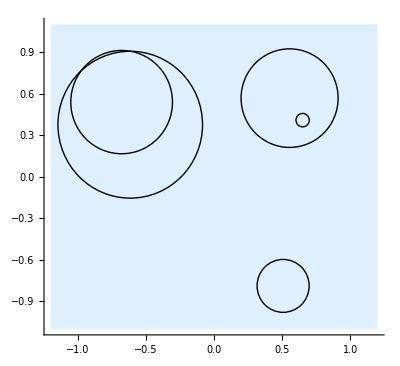

```mathematica
showRandomCircles[list, 1.2,1.1]
```

c.

```mathematica
(*  This function returns a modified list of circles, which includes only the circles that do not include the specified point within their bounds  *)uRemoveCircles[circlelst_, pt_]:= Module[{clist = circlelst,reslist = {}, ptx = pt[[1]], pty = pt[[2]], ptdistance, i = 1},
For[
i, i ≤ Length[circlelst], i++,
ptdistance =Sqrt[(ptx-clist[[i, 1, 1]])^2+(pty-clist[[i, 1,2]])^2];
If[ptdistance > clist[[i, 2]],
AppendTo[reslist, clist[[i]]]
]
];
Return[reslist];
]
```

```mathematica
pointexample = {-0.75, 0.5};
```

```mathematica
uRemoveCircles[list, pointexample]
```

{{{0.650665,0.407838},0.0486157},{{0.50741,-0.789889},0.191129},{{0.554954,0.566971},0.356147}}

d.

```mathematica
(*This Module displays the circles on a light blue backdrop, this time with colors which reflect how many times they intersect other circles. The colors Blue,Red,Green,Yellow,Purple,Orange are used to draw circles which intersect 1,2,3,4,5,or more than 5 circles drawn.   Note: CC stands for current circle and OC stands for other circle.*)
uColorOverlappingCircles[circlelst_, xbound_, ybound_]:= Module[{count, OCcount, numIntrsct, list = circlelst, radCC, xB = xbound, yB = ybound, xCC, yCC, yOC, xOC, radOC, graphicsList = {}},
AppendTo[graphicsList, LightBlue];
AppendTo[graphicsList, Rectangle[{-xB, -yB}, {xB, yB}]];

(* Loop that goes through all the circles in the list *)

For[count = 1, count ≤ Length[list], count++,

radCC = list[[count, 2]];
xCC = list[[count, 1, 1]];
yCC = list[[count, 1, 2]];
numIntrsct = 0;
	

	(* This loop finds the  number of intersection points of each circle by comparing it to every other circle. *)
	For[OCcount = 1, OCcount≤ Length[list], OCcount++,
	xOC = list[[OCcount, 1, 1]];  
	yOC=list[[OCcount, 1,2]]; 
	radOC=list[[OCcount, 2]];
	If[ (xOC-xCC)^2+(yOC-yCC)^2<(radOC+radCC)^2 && !(OCcount==count) && !withinQ[xOC, yOC, radOC, xCC, yCC, radCC], numIntrsct+=2];
	If[ (xOC-xCC)^2+(yOC-yCC)^2==(radOC+radCC)^2 && !(OCcount==count) &&!withinQ[xOC, yOC, radOC, xCC, yCC, radCC], numIntrsct+=1; ];
	];
(*Now that the numIntrsct variable is known for the current circle, the color is set (by adding it to the graphingList) accordingly.*)
If[numIntrsct==0,
AppendTo[graphicsList, Black]]; 
If[numIntrsct==1,
AppendTo[graphicsList, Blue]]; 
If[numIntrsct==2,
AppendTo[graphicsList, Red]];
 If[numIntrsct==3,
AppendTo[graphicsList, Green]]; 
If[numIntrsct==4,
AppendTo[graphicsList, Yellow]]; 
If[numIntrsct==5,
AppendTo[graphicsList, Purple]];
If[numIntrsct>5,
AppendTo[graphicsList, Orange]];  
AppendTo[graphicsList,Circle[{list[[count, 1, 1]], list[[count, 1, 2]]}, list[[count, 2]]]]
];
Graphics[graphicsList, Axes -> True]
]
```

```mathematica
(*This function returns a boolean as to whether one of the two circles about which information is given is contained in the other.*)
withinQ[xOne_, yOne_, radOne_, xTwo_, yTwo_, radTwo_]:=Module[{x1=xOne, y1=yOne, rad1=radOne, x2=xTwo, y2=yTwo, rad2=radTwo}, If[√((x1-x2)^2+(y1-y2)^2)+ rad1 < rad2 || √((x1-x2)^2+(y1-y2)^2)+ rad2 < rad1, Return[True], Return[False]]
]
```

```mathematica
circleLiSt = {{{-0.6149299199518321,0.3750434565824383},0.5306882930962631},{{-0.6781541939721194,0.5383835071914094},0.37328372429911716},{{0.6506654529466394,0.4078377365422208},0.04861565584805583},{{0.5074097159075928,-0.7898889806434637},0.19112869516612951},{{0.5549539216177939,0.5669709296440084},0.35614693742990533}};
```

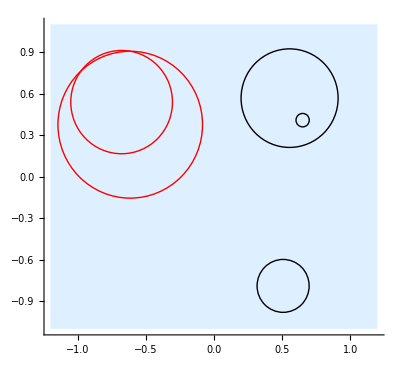

```mathematica
uColorOverlappingCircles[circleLiSt, 1.2, 1.1]
```

3.

i.

```mathematica
(*This function displays a purple polygon with the given number of sides and side length.*)
uRegPoly[length_, n_] :=Module[{lengthS=length,radius, count,  num=n, list={}}, 
radius= Sin[(180-360/num)/2 Degree]/(Sin[360/num Degree]/lengthS); 
For [ count=0,count< num, count++, 
AppendTo[list,{radius*Cos[(360*count)/num Degree], radius*Sin[(360*count)/num Degree]}]]; 
Graphics[ {Purple, Polygon[list]},Axes -> True
] 
]
```

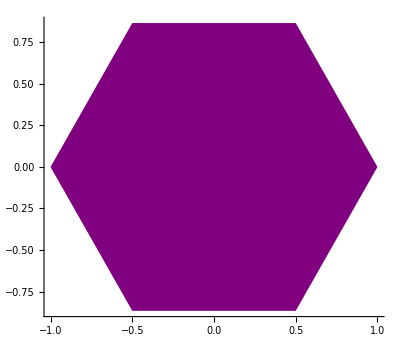

```mathematica
uRegPoly[1, 6]
```

```mathematica
ii.
```

```mathematica
(*The function uRegPyram diaplays a pyramid with the base as the polygon generated in uRegPolyBase (a hybrid of uRegPoly above).*)
uRegPolyBase[length_, n_] :=Module[{lengthS=length,radius, count,  num=n, list={}}, 
radius= Sin[(180-360/num)/2 Degree]/(Sin[360/num Degree]/lengthS); 
For [ count=0,count< num, count++, 
AppendTo[list,{radius*Cos[(360*count)/num Degree], radius*Sin[(360*count)/num Degree], 0}]]; 
Return[list] 
]
```

```mathematica
uRegPyram[length_, n_, height_] :=Module[{lengthS=length, listLength, count,  num=n,lineList = {},  slantHeight,radius, heightS=height, list}, 

list = uRegPolyBase[lengthS, num];
radius= Sin[(180-360/num)/2 Degree]/(Sin[360/num Degree]/lengthS);
AppendTo[list, {0, 0, heightS}];

For[count = 1, count ≤ Length[list], count++,
AppendTo[lineList, count];
];

listLength = Length[list];

For[count = 1, count< Length[list], count++,
AppendTo[lineList, count];
AppendTo[lineList, listLength];
];

Print[lineList];
AppendTo[lineList, 1];
AppendTo[lineList,  Length[list]-1]; 
Show[Graphics3D[GraphicsComplex[list,Polygon[{lineList}]]], Boxed-> False, Axes->True]
]
```

```mathematica
uRegPyram[4, 4, 4]
```

{1,2,3,4,5,1,5,2,5,3,5,4,5}

-Graphics3D-

iii.

```mathematica
(*This function displays two pyramids like the one displayed by uRegPyram attached to each other at the base.*)
uTwoRegPyram[sidelength_, numberofsides_, height_] := Module[
{l = sidelength, n = numberofsides, h = height, list = {}, lineList = {},count, listLength},
  
(* This part of the code is responsible for adding to the list the number of vertices *)
list = uRegPolyBase[l, n];
AppendTo[list, {0, 0, h}];
For[count = 1, count ≤ Length[list]-1, count++,
AppendTo[lineList, count];
];
AppendTo[lineList, 1];
AppendTo[lineList,  Length[list]];

(* This part of the code adds the sequence of vertices to connect the sides of the upper pyramid *)
listLength = Length[list];
For[count = 1, count≤ Length[list], count++,
AppendTo[lineList, count];
AppendTo[lineList, listLength];
];

(* This part of the code adds the negative height *)
AppendTo[list, {0, 0, -h}];
AppendTo[lineList, {0, 0, -h}];
For[count = 1, count ≤ Length[list]-1, count++,
AppendTo[lineList, count];
AppendTo[lineList, Length[list]]];

Show[Graphics3D[{Green,GraphicsComplex[list,Polygon[{lineList}]]}], Boxed-> False, Axes -> True]
]
```

```mathematica
uTwoRegPyram[7, 6,  12]
```

-Graphics3D-